```mathematica
GenerateRandomMatrix[b_]:=RandomReal[{0,.25},{Round[b],Round[b]}]+DiagonalMatrix[RandomReal[{.6,.75},Round[b]]];
GenerateRandomMatrix3[b_]:=If[Round[(0.8-(Pi/b))*5]>0,RandomReal[{0,.25},{Round[b],Round[b]}]+DiagonalMatrix[RandomReal[{.6,.75},Round[b]]]+DiagonalMatrix[RandomReal[{.3,.45},Round[b]],Table[i,{i,1,Round[(0.8-(Pi/b))*5]}]][[1;;Round[b],1;;Round[b]]]+DiagonalMatrix[RandomReal[{.3,.45},Round[b]],Table[-i,{i,1,Round[(0.8-(Pi/b))*5]}]][[1;;Round[b],1;;Round[b]]],RandomReal[{0,.25},{Round[b],Round[b]}]+DiagonalMatrix[RandomReal[{.6,.75},Round[b]]]];

ColorFun[cin_,ain_,b_]:=With[{a=Mod[Round[ain*(b-1)/2/Pi],(b-1)]+1,c=Mod[Round[cin*(b-1)/2/Pi],(b-1)]+1,confMat=RandomReal[{0,1},{Round[b],Round[b]}]},With[{partVal=Part[confMat,Round[a],Round[c]]},If[a==c,{partVal,Round[a],Round[c],RGBColor[{0,1,0}]},{partVal,Round[a],Round[c],RGBColor[{1,0,0}]}]]];
ColorFunMatrix[cin_,ain_,b_,confMat_]:=With[{borderline=.05},With[{a=Mod[Round[ain*(b-1)/2/Pi],(b-1)]+1,c=Mod[Round[cin*(b-1)/2/Pi],(b-1)]+1},With[{partVal=Part[confMat,Round[a],Round[c]]},If[Mod[ain,2Pi/(b-1)]+b/2<borderline ||Mod[cin,2Pi/(b-1)]+b/2<borderline,{1,RGBColor[{0,0,0}]}, If[a==c,{1,Round[a],Round[c],RGBColor[partVal*{0,1,0}+(1-partVal)*{1,1,1}]},{1,Round[a],Round[c],RGBColor[partVal*{1,0,0}+(1-partVal)*{1,1,1}]}]]]]];
v3[a_,b_,θin_,ϕin_]:=With[{ϕ=ϕin(*Round[ϕin*b]/b*),θ=θin},{(a+b*Cos[θ])*Cos[ϕ],(a+b*Cos[θ])*Sin[ϕ],a*Sin[θ]}]
v4[a_,b_,θin_,ϕin_]:=With[{ϕ=ϕin(*Round[ϕin*b]/b*),θ=θin(*Round[θin*b/2/Pi]/b*2*Pi*)},{(a+b*Cos[θ])*Cos[θ],(a+b*Cos[θ])*Sin[θ],a*Sin[θ]}]
v5[a_,b_,θin_,ϕin_]:=With[{ϕ=ϕin(*Round[ϕin*b]/b*),θ=θin},{(a+b*Cos[θ+ϕ])*Cos[ϕ],(a+b*Cos[θ+ϕ])*Sin[ϕ],a*Sin[θ+ϕ]}]
Manipulate[With[{a=2*b,thickval=0.01,confMat=GenerateRandomMatrix[b]},Show[{ParametricPlot3D[v5[a,b,θ,ϕ],{θ,-Pi(*ϕ-2*(2*Pi/b)*),Pi(*ϕ+2*(2*Pi/b)*)},{ϕ,startphi,endphi},ColorFunction->Function[{x,y,z,θ,ϕ},Directive[Opacity[First@ColorFunMatrix[ϕ,ϕ+θ,b,confMat]],Last@ColorFunMatrix[ϕ,ϕ+θ,b,confMat]]],ColorFunctionScaling->False,PlotPoints->100,Mesh->{b*2,(b-1)*2},MeshFunctions->{#4+#5&,#5&},MeshStyle->{{Thickness[thickval], Black},{Thickness[thickval], Black}}]},ImageSize->Large]],{{b,14},3,14,1},{startphi,-Pi,Pi},{endphi,Pi,2*Pi}]
```

```mathematica
Show[Flatten[{Table[With[{a=b*5},ParametricPlot3D[{0,0,5b}+v4[a,b,θ,θ],{θ,0,2*Pi},PlotStyle->{Black,Thickness[.02]}]],{b,10,1,-1}],Table[With[{a=b*5},ParametricPlot3D[{0,0,5b}+v5[a,b,θ,ϕ],{θ,-Pi/8,Pi/8},{ϕ,0,2*π},ColorFunction->Function[{x,y,z,θ},Hue[θ]]]],{b,10,1,-1}]}]]
```

-Graphics3D-

```mathematica
Manipulate[With[{thickval=0.02},ParametricPlot[With[{t=tin(*Round[tin*b/2/Pi]/b*2*Pi*)},r^2 {Cos[t],Sin[t]}],{tin,0, 2Pi},{r,1,2},ColorFunction->Function[{x,y,θ,r},Hue[(r-1.5)]],Mesh->{b-1,b-1},MeshStyle->{{Thickness[thickval], Black},{Thickness[thickval], Black}}]],{b,3,10,1}]
```

```mathematica
Show[With[{thickval=0.005},Flatten[{Table[ParametricPlot[With[{t=tin(*Round[tin*b/2/Pi]/b*2*Pi*)},r^2 {Cos[t],Sin[t]}],{tin,0, 2Pi},{r,2*b,2*b+1},ColorFunction->Function[{x,y,θ,r},Hue[(r-1.5)]],Mesh->{b-1,b-1},MeshStyle->{{Thickness[thickval], Black},{Thickness[thickval], Black}}],{b,14,1,-1}]}]],ImageSize->Full]
```

-Graphics-

```mathematica
ColorFun[1]
```

ColorFun[1]

```mathematica
Manipulate[ColorFun[a],{a,-2,2}]
```

```mathematica
RandomReal[{0,1},{4,4}]
```

{{0.421774,0.671912,0.34922,0.282223},{0.229206,0.0105646,0.407151,0.207473},{0.877359,0.985933,0.6683,0.683511},{0.530806,0.174946,0.99789,0.614494}}

```mathematica
Manipulate[ColorFun[aa*2*Pi,bb*2*Pi,cc],{aa,0,1},{bb,0,1},{cc,4,8,1}]
```

```mathematica
N[1/5]
```

0.2

```mathematica
1-.832
```

0.168

```mathematica
1/0.16800000000000004
```

5.95238

```mathematica
M={{0.7895860035080238,0.9082579769780073,0.08258391072996818,0.024579978472902386},{0.2737942872665202,0.3216088262833654,0.6253501090742035,0.2771360639607152},{0.9972442264385422,0.3586945843216367,0.4530715428295493,0.9701489418749702},{0.6107877732798279,0.03689581465745784,0.12384067780664387,0.9424494329317834}};
```

```mathematica
M[[1,4]]
```

0.02458

```mathematica
Manipulate[With[{confMat=GenerateRandomMatrix[cc]},Plot3D[First@ColorFunMatrix[aa*2*Pi,bb*2*Pi,cc,confMat],{aa,0,1},{bb,0,1},ColorFunctionScaling->True,ColorFunction->Function[{x,y,z,aa,bb},Last@ColorFunMatrix[aa,bb,cc,confMat]]]],{cc,4,8,1}]
```

Part::pkspec1: The expression Round[1+Mod[Round[(3 bb$)/(2 π)],3]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
GenerateRandomMatrix[4]
```

{{0.910133,0.132256,0.149928,0.0248872},{0.0100194,0.844542,0.248714,0.0643494},{0.00288642,0.187061,0.877876,0.229529},{0.206834,0.181532,0.0874859,0.803362}}

```mathematica
Show[Graphics[InsetMatrix[GenerateRandomMatrix[5],3*5,5]]]
```

-Graphics-

```mathematica
Evaluate[GenerateRandomMatrix[5]]
```

{{0.837979,0.129054,0.114183,0.238109,0.0727697},{0.0947128,0.781674,0.146116,0.148327,0.228656},{0.194656,0.215127,0.720263,0.0439956,0.239445},{0.0655746,0.0488884,0.0188112,0.70234,0.046891},{0.182122,0.133451,0.119222,0.0803902,0.693199}}

```mathematica
DiagonalMatrix[RandomReal[{.3,.55},Round[4]],-1]+DiagonalMatrix[RandomReal[{.3,.55},Round[b]],1]
```

RandomReal::array: The array dimensions Round[b] given in position 2 of RandomReal[{0.3,0.55},Round[b]] should be a list of non-negative machine-sized integers giving the dimensions for the result.

{{0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1]},{0.443395+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1]},{0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.502356+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1]},{0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.413277+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1]},{0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.473322+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1],0.+DiagonalMatrix[RandomReal[{0.3,0.55},Round[b]],1]}}

```mathematica
GenerateRandomMatrixW DiagBand[b_]:=RandomReal[{0,.25},{Round[b],Round[b]}]+DiagonalMatrix[RandomReal[{.6,.75},Round[b]]]+DiagonalMatrix[RandomReal[{.2,.45},Round[b]],-1];
```

SetDelayed::write: Tag Times in GenerateRandomMatrixW DiagBand[b_] is Protected.

```mathematica
GenerateRandomMatrixW DiagBand[4]
```

GenerateRandomMatrixW DiagBand[4]

```mathematica
Manipulate[With[{confMat=GenerateRandomMatrix2[b]},Show[{ParametricPlot[{Cos[theta]*r,Sin[theta]*r},{theta,0,2*Pi},{r,1,2*Pi+1},Mesh->{b*withVal,b*withVal},MeshShading->GetMatrixC[withVal],ColorFunction->Function[{x,y,u,vin},With[{v=vin},Directive[Opacity[1],With[{vPos=Min[Floor[b],Mod[Floor[(Mod[(v-1)/2/Pi,1]+Floor[b*Mod[(u-Pi)/2/Pi,1]]/b)*b],b]+1],uPos=Min[Floor[b],Floor[Mod[u/2/Pi,1]*b]+1]},With[{alphaVal=confMat[[vPos,uPos]]},Hue[vPos/b]]]]]],ColorFunctionScaling->False],ParametricPlot[{Cos[theta]*r,Sin[theta]*r},{theta,0,2*Pi},{r,1,2*Pi+1},Mesh->{b*withVal,b*withVal},MeshShading->GetMatrixU[withVal],ColorFunction->Function[{x,y,u,v},Hue[Mod[u/2/Pi,1]]],ColorFunctionScaling->False],ParametricPlot[{Cos[theta]*r,Sin[theta]*r},{theta,0,2*Pi},{r,1,2*Pi+1},Mesh->{b*withVal,b*withVal},MeshShading->GetMatrixV[withVal],ColorFunction->Function[{x,y,u,v},Hue[Mod[(v-1)/2/Pi,1]+Floor[b*Mod[(u-Pi)/2/Pi,1]]/b]],ColorFunctionScaling->False]}]],{{b,5},4,20,1},{{withVal,5},5,25,1}]
```

```mathematica
Manipulate[Manipulate[With[{withVal2=40,confMat=GenerateRandomMatrix2[b]},Show[{ParametricPlot[{theta,2*Pi-r},{theta,0,2*Pi},{r,0,2*Pi},Mesh->{b*withVal,b*withVal},MeshShading->GetMatrixC[withVal],MeshStyle->GetMatrixCMesh[b*withVal],ColorFunction->Function[{x,y,u,vin},With[{v=vin},Directive[Opacity[1],With[{vPos=Min[Floor[b],Mod[Floor[Mod[(v)/2/Pi,1]*b],b]+1],uPos=Min[Floor[b],Floor[Mod[u/2/Pi,1]*b]+1]},With[{alphaVal=confMat[[vPos,uPos]]},If[Abs[vPos-uPos]<1(*Abs[Floor[Mod[v*b,b]]-Floor[Mod[u*b,b]]]<1/b/b*)(*Abs[u-v]<1/2/Pi*),RGBColor[alphaVal*{0,1,0}+(1-alphaVal)*{1,1,1}],RGBColor[alphaVal*{1,0,0}+(1-alphaVal)*{1,1,1}]]]]]]],ColorFunctionScaling->False],ParametricPlot[{theta,2*Pi-r},{theta,0,2*Pi},{r,0,2*Pi},Mesh->{b*withVal,b*withVal},MeshShading->GetMatrixU[withVal],ColorFunction->Function[{x,y,u,v},Hue[Mod[u/2/Pi,1]]],ColorFunctionScaling->False],ParametricPlot[{theta,2*Pi-r},{theta,0,2*Pi},{r,0,2*Pi},Mesh->{b*withVal,b*withVal},MeshShading->GetMatrixV[withVal],MeshStyle->None,ColorFunction->Function[{x,y,u,v},Hue[Mod[(v)/2/Pi,1]]],ColorFunctionScaling->False],ParametricPlot[{theta,2*Pi-r},{theta,2*Pi/(b)*(selectU-1),2*Pi/(b)*selectU},{r,2*Pi/b*(selectV-1),2*Pi/b*selectV},Mesh->{withVal2,withVal2},MeshShading->GetMatrixSelect[withVal2],MeshStyle->None,ColorFunction->Function[{x,y,u,v},RGBColor[{0,0,0}]],ColorFunctionScaling->False]},ImageSize->Large]],{selectU,1,b,1},{selectV,1,b,1}],{{b,6},4,20,1},{{withVal,5},5,25,1}]
```

```mathematica
Manipulate[Manipulate[With[{withVal2=40,confMat=GenerateRandomMatrix2[b]},Show[{ParametricPlot[{Cos[theta]*r,Sin[theta]*r},{theta,0,2*Pi},{r,1,2*Pi+1},Mesh->{b*withVal,b*withVal},MeshShading->GetMatrixC[withVal],MeshStyle->GetMatrixCMesh[b*withVal],ColorFunction->Function[{x,y,u,vin},With[{v=vin},Directive[Opacity[1],With[{vPos=Min[Floor[b],Mod[Floor[(Mod[(v-1)/2/Pi,1]+Floor[b*Mod[(u-Pi)/2/Pi,1]]/b)*b],b]+1],uPos=Min[Floor[b],Floor[Mod[u/2/Pi,1]*b]+1]},With[{alphaVal=confMat[[vPos,uPos]]},If[Abs[vPos-uPos]<1(*Abs[Floor[Mod[v*b,b]]-Floor[Mod[u*b,b]]]<1/b/b*)(*Abs[u-v]<1/2/Pi*),RGBColor[alphaVal*{0,1,0}+(1-alphaVal)*{1,1,1}],RGBColor[alphaVal*{1,0,0}+(1-alphaVal)*{1,1,1}]]]]]]],ColorFunctionScaling->False],ParametricPlot[{Cos[theta]*r,Sin[theta]*r},{theta,0,2*Pi},{r,1,2*Pi+1},Mesh->{b*withVal,b*withVal},MeshShading->GetMatrixU[withVal],ColorFunction->Function[{x,y,u,v},Hue[Mod[u/2/Pi,1]]],ColorFunctionScaling->False],ParametricPlot[{Cos[theta]*r,Sin[theta]*r},{theta,0,2*Pi},{r,1,2*Pi+1},Mesh->{b*withVal,b*withVal},MeshShading->GetMatrixV[withVal],MeshStyle->None,ColorFunction->Function[{x,y,u,v},Hue[Mod[(v-1)/2/Pi,1]+Floor[b*Mod[(u-Pi)/2/Pi,1]]/b]],ColorFunctionScaling->False],ParametricPlot[{Cos[theta]*r,Sin[theta]*r},{theta,2*Pi/(b)*(selectU-1),2*Pi/(b)*selectU},{r,2*Pi/b*(selectV-1)+1,2*Pi/b*selectV+1},Mesh->{withVal2,withVal2},MeshShading->GetMatrixSelect[withVal2],MeshStyle->None,ColorFunction->Function[{x,y,u,v},RGBColor[{0,0,0}]],ColorFunctionScaling->False]},ImageSize->Large]],{selectU,1,b,1},{selectV,1,b,1}],{{b,6},4,20,1},{{withVal,5},5,25,1}]
```

```mathematica
Manipulate[Manipulate[Manipulate[With[{withVal2=40,useAlpha=1,a=3*b,thickval=0.01,confMat=GenerateRandomMatrix2[b]},Show[{ParametricPlot3D[v5[a,b,θ,ϕ],{θ,-Pi(*ϕ-2*(2*Pi/b)*),Pi(*ϕ+2*(2*Pi/b)*)},{ϕ,-Pi,Pi},ColorFunctionScaling->False,ColorFunction->Function[{x,y,z,u,v},Directive[Opacity[1],With[{vPos=Min[Round[b],Floor[Mod[v/2/Pi*b,b]]+1],uPos=Min[Round[b],Floor[Mod[u/2/Pi*b,b]]+1]},With[{alphaVal=confMat[[vPos,uPos]]},If[Abs[vPos-uPos]<1(*Abs[Floor[Mod[v*b,b]]-Floor[Mod[u*b,b]]]<1/b/b*)(*Abs[u-v]<1/2/Pi*),RGBColor[alphaVal*{0,1,0}+(1-alphaVal)*{1,1,1}],RGBColor[alphaVal*{1,0,0}+(1-alphaVal)*{1,1,1}]]]]]],MeshFunctions->{#4&,#5&},MeshStyle->None,MeshShading->GetMatrixC[withVal],Mesh->{Round[b]*withVal,Round[b]*withVal}],ParametricPlot3D[v5[a,b,θ,ϕ],{θ,-Pi(*ϕ-2*(2*Pi/b)*),Pi(*ϕ+2*(2*Pi/b)*)},{ϕ,-Pi,Pi},ColorFunction->Function[{x,y,z,u,v},Hue[Mod[v/2/Pi,1]]],ColorFunctionScaling->False,MeshFunctions->{#4&,#5&},MeshStyle->None,MeshShading->GetMatrixV[withVal],Mesh->{Round[b]*withVal,Round[b]*withVal}],ParametricPlot3D[v5[a,b,θ,ϕ],{θ,-Pi(*ϕ-2*(2*Pi/b)*),Pi(*ϕ+2*(2*Pi/b)*)},{ϕ,-Pi,Pi},ColorFunction->Function[{x,y,z,u,v},Hue[Mod[u/2/Pi,1]]],ColorFunctionScaling->False,MeshFunctions->{#4&,#5&},MeshStyle->None,MeshShading->GetMatrixU[withVal],Mesh->{Round[b]*withVal,Round[b]*withVal}],ParametricPlot3D[v5[a,b,θ,ϕ],{θ,2*Pi/(b-1)*(selectU-1),2*Pi/(b-1)*selectU},{ϕ,2*Pi/b*(selectV-1)+1,2*Pi/b*selectV+1},Mesh->{withVal2,withVal2},MeshShading->GetMatrixSelect[withVal2],MeshStyle->None,ColorFunction->Function[{x,y,z,u,v},RGBColor[{0,0,0}]],ColorFunctionScaling->False]},ImageSize->Medium]],{selectU,1,b,1},{selectV,1,b,1}],{{b,7},4,14},{{withVal,8},5,25,1}],{viewpoint,0,2Pi,0.01}]
```

```mathematica
Mod[{-1,0,1,2,3,4,5,6,7},4]
```

{3,0,1,2,3,0,1,2,3}

```mathematica
With[{b=5},Plot3D[With[{vPos=Floor[Mod[v/2/Pi*b,b]]+1,uPos=Floor[Mod[u/2/Pi*b,b]]+1},Abs[vPos-uPos]],{u,-Pi,Pi},{v,-Pi,Pi},ColorFunction->Function[{x,y,z},Hue[z]]]]
```

-Graphics3D-

```mathematica
Table[Automatic,{i,1,5}]
```

{Automatic,Automatic,Automatic,Automatic,Automatic}

```mathematica
GetMatrixU[width_]:=With[{aMat=Table[Automatic,{i,1,width},{j,1,width}],bMat=Table[None,{i,1,width},{j,1,width}]},With[{result=Join[List/@aMat[[1;;width,1]],bMat[[1;;width,2;;width]],2]},
result]]
GetMatrixSelect[width_]:=If[width<4,Table[None,{i,1,width},{j,1,width}],Table[If[(Abs[i-j]<width/8)||(Abs[i-(width+1-j)]<width/8),Automatic,None],{i,1,width},{j,1,width}]];
GetMatrixSelect2[width_]:=If[width<4,Table[None,{i,1,width},{j,1,width}],Table[If[(i==2&&j>1&&j<=width)||(i==width&&j>1&&j<=width)||(j==2&&i>1&&i<=width)||(j==width&&i>1&&i<=width),Automatic,None],{i,1,width},{j,1,width}]];
```

```mathematica
GetMatrixUMesh[width_]:=With[{aMat=Table[Opacity[0],{i,1,width},{j,1,width}],bMat=Table[Black,{i,1,width},{j,1,width}]},With[{result=Join[List/@aMat[[1;;width,1]],bMat[[1;;width,2;;width]],2]},
result]]
```

```mathematica
GetMatrixUInv[width_]:=With[{aMat=Table[None,{i,1,width},{j,1,width}],bMat=Table[Automatic,{i,1,width},{j,1,width}]},With[{result=Join[List/@aMat[[1;;width,1]],bMat[[1;;width,2;;width]],2]},
result]]
GetMatrixUInvMesh[width_]:=With[{aMat=Table[Black,{i,1,width},{j,1,width}],bMat=Table[Opacity[0],{i,1,width},{j,1,width}]},With[{result=Join[List/@aMat[[1;;width,1]],bMat[[1;;width,2;;width]],2]},
result]]
```

```mathematica
GetMatrixU[4]
```

{{Automatic,None,None,None},{Automatic,None,None,None},{Automatic,None,None,None},{Automatic,None,None,None}}

```mathematica
GetMatrixV[width_]:=Transpose[GetMatrixU[width]]
GetMatrixVInv[width_]:=Transpose[GetMatrixUInv[width]]
GetMatrixVMesh[width_]:=Transpose[GetMatrixUMesh[width]]
GetMatrixVInvMesh[width_]:=Transpose[GetMatrixUInvMesh[width]]
```

```mathematica
GetMatrixV[4]
```

{{Automatic,Automatic,Automatic,Automatic},{None,None,None,None},{None,None,None,None},{None,None,None,None}}

```mathematica
GetMatrixC[width_]:=With[{bMat=Transpose[GetMatrixUInv[width]],aMat=Table[None,{i,1,width},{j,1,width}]},With[{result=Join[List/@aMat[[1;;width,1]],bMat[[1;;width,2;;width]],2]},result]]
GetMatrixCMesh[width_]:=With[{bMat=Transpose[GetMatrixUInvMesh[width]],aMat=Table[Black,{i,1,width},{j,1,width}]},With[{result=Join[List/@aMat[[1;;width,1]],bMat[[1;;width,2;;width]],2]},result]]
```

```mathematica
GetMatrixC[4]
```

{{None,None,None,None},{None,Automatic,Automatic,Automatic},{None,Automatic,Automatic,Automatic},{None,Automatic,Automatic,Automatic}}

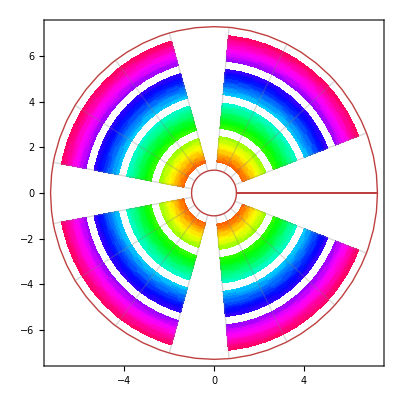

```mathematica
ParametricPlot[{Cos[theta]*r,Sin[theta]*r},{theta,0,2*Pi},{r,1,2*Pi+1},Mesh->{4*4,4*4},MeshShading->{{None,None,None,None},{None,Automatic,Automatic,Automatic},{None,Automatic,Automatic,Automatic},{None,Automatic,Automatic,Automatic}},MeshStyle->{{Black,Black,Black,Black},{Black,Opacity[0],Opacity[0],Opacity[0]},{Black,Opacity[0],Opacity[0],Opacity[0]},{Black,Opacity[0],Opacity[0],Opacity[0]}},ColorFunction->Function[{x,y,u,vin},Hue[vin]]]
```

```mathematica
GetMatrixSelect[9]
```

{{Automatic,Automatic,None,None,None,None,None,Automatic,Automatic},{Automatic,Automatic,Automatic,None,None,None,Automatic,Automatic,Automatic},{None,Automatic,Automatic,Automatic,None,Automatic,Automatic,Automatic,None},{None,None,Automatic,Automatic,Automatic,Automatic,Automatic,None,None},{None,None,None,Automatic,Automatic,Automatic,None,None,None},{None,None,Automatic,Automatic,Automatic,Automatic,Automatic,None,None},{None,Automatic,Automatic,Automatic,None,Automatic,Automatic,Automatic,None},{Automatic,Automatic,Automatic,None,None,None,Automatic,Automatic,Automatic},{Automatic,Automatic,None,None,None,None,None,Automatic,Automatic}}

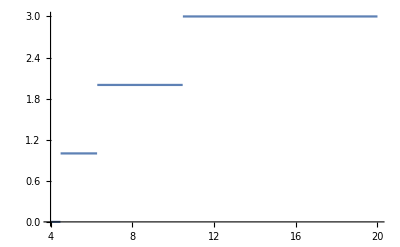

```mathematica
Plot[Round[(0.8-(Pi/b))*5],{b,4,20}]
```

```mathematica
GenerateRandomMatrix2[5]
```

{{0.960005,0.0362384,0.283826,0.271434,0.0615852},{0.310731,0.759917,0.143123,0.0754208,0.0441472},{0.0323402,0.346653,0.923093,0.189449,0.218621},{0.00414176,0.164371,0.0308469,0.715641,0.185001},{0.250347,0.0421597,0.267037,0.238593,0.814635}}

```mathematica
GenerateRandomMatrix2[b_]:=With[{ColDistVal=9Pi/32},Table[With[{angDist=Evaluate[ArcTan[Sin[x/b*2Pi-y/b*2Pi],Cos[x/b*2Pi-y/b*2Pi]]-Pi/2]},If[Abs[angDist]<ColDistVal,RandomReal[{0.7,0.99}],RandomReal[{0.0,0.35}]]],{x,1,b},{y,1,b}]]
```

```mathematica
GenerateRandomMatrix2[8]
```

{{0.758925,0.890558,0.142267,0.334371,0.277879,0.246272,0.156522,0.731354},{0.963857,0.852012,0.956351,0.202088,0.0316946,0.311095,0.0802023,0.215628},{0.29307,0.755869,0.755469,0.965488,0.188333,0.0585428,0.0343947,0.0494205},{0.090884,0.260128,0.815296,0.796905,0.754063,0.33423,0.0816226,0.125634},{0.183658,0.0461189,0.31462,0.730222,0.873138,0.866585,0.0922126,0.154263},{0.148916,0.344628,0.0123022,0.124116,0.706815,0.886061,0.715057,0.0245548},{0.240459,0.231474,0.102295,0.205302,0.303431,0.8075,0.882567,0.79008},{0.93893,0.24714,0.127142,0.0137179,0.256295,0.337503,0.718777,0.917587}}